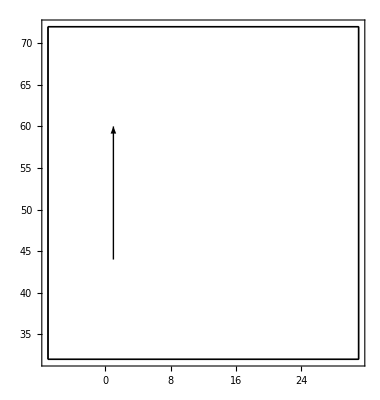

```mathematica
Graphics[Arrow[{{7,44},{7,60},{1,60}}],Frame->True];
Graphics[Arrow[{{1,44},{1,60}}],Frame->True];
LP = Graphics[Line[{{{-7,32},{31,32}},{{-7,32},{-7,72}},{{-7,72},{31,72}},{{31,72},{31,32}}}],Frame->True];
Show[%,%%,LP]
```

```mathematica
Evolucion1 = Import["/home/apu/Desktop/Proyecto Transporte/Simu/Github/Prueba1","CSV"];
```

```mathematica
iteracion = 12 (*Numero de iteraciones que hago con el codigo python*);
```

```mathematica
Table[
Show[Graphics[
Arrow[{
{Evolucion1[[i]][[1]],Evolucion1[[i]][[2]]},
{Evolucion1[[i]][[3]],Evolucion1[[i]][[4]]}}],
Frame->True],LP]
,{i,2,iteracion}];
```

```mathematica
ListAnimate[%]
```

```mathematica
Evolucion1 = Import["/home/apu/Desktop/Proyecto Transporte/Simu/Github/Prueba2","CSV"];
```

```mathematica
iteracion = 10 (*Numero de iteraciones que hago con el codigo python*);
```

```mathematica
Table[
Show[Graphics[
Arrow[{
{Evolucion1[[i]][[1]],Evolucion1[[i]][[2]]},
{Evolucion1[[i]][[3]],Evolucion1[[i]][[4]]}}],
Frame->True],LP]
,{i,1,iteracion}];
```

```mathematica
ListAnimate[%]
```

```mathematica
Evolucion1 = Import["/home/apu/Desktop/Proyecto Transporte/Simu/Github/Prueba3","CSV"];
```

```mathematica
iteracion = 40 (*Numero de iteraciones que hago con el codigo python*);
```

```mathematica
Table[
Show[Graphics[
Arrow[{
{Evolucion1[[i]][[1]],Evolucion1[[i]][[2]]},
{Evolucion1[[i]][[3]],Evolucion1[[i]][[4]]}}],
Frame->True],LP]
,{i,1,iteracion}];
```

```mathematica
ListAnimate[%]
```

```mathematica
Expor["Animacion.jpg2",%12]
```

Expor[Animacion.jpg2,]